# HHListLinePlotMean Tests

```mathematica
<<HokahokaW`
```

HokahokaW`HHPackageGitLoad: Loaded Git repository located at C:\prog\_w\HokahokaW\.git

HokahokaW`
Tue 20 Oct 2015 22:59:09     [Mathematica: 10.3.0 for Microsoft Windows (64-bit) (October 9, 2015)]
     Current local repository path:   C:\prog\_w\HokahokaW\.git
     Current branch [hash]:  dev [bc911f1d68c5a4063caa037903f5428a07ec270e]
     Remote:  origin (https://ktakagaki@github.com/ktakagaki/HokahokaW.git)

```mathematica
testData = Table[ Table[ Sin[x* 2 Pi]*RandomReal[{0.9,1/0.9}]+RandomReal[{-2,2}], {x,0,1.5,0.01}],{100}];
```

```mathematica
Options[HHListLinePlotMean]
```

{HHMeanPlot→True,HHMeanPlotStyle→{Opacity[0.5,GrayLevel[0]]},HHErrorPlot→True,HHErrorPlotStyle→None,HHErrorPlotFillingStyle→Opacity[0.25,RGBColor[0, 0, 1]],PlotStyle→None,AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→True,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

## You can plot either the standard error (default) or the standard deviation

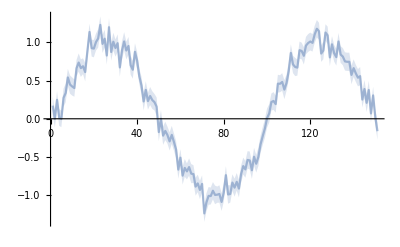

```mathematica
HHListLinePlotMean[ testData ]
```

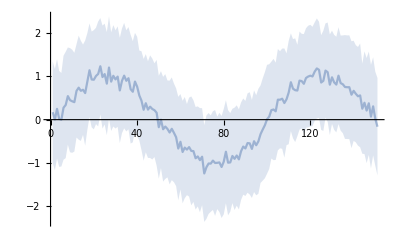

```mathematica
HHListLinePlotMean[ testData, HHErrorPlot-> "StandardDeviation"]
```

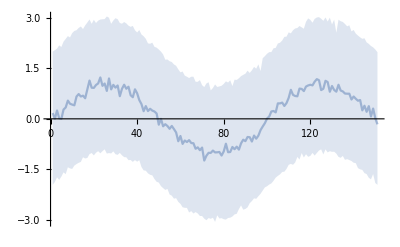

```mathematica
HHListLinePlotMean[ testData, HHErrorPlot-> MinMax]
```

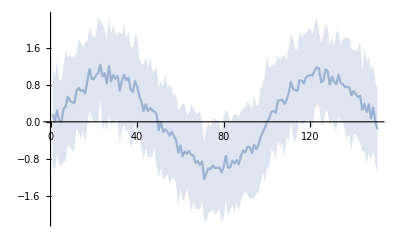

```mathematica
HHListLinePlotMean[ testData, HHErrorPlot-> Quartiles]
```

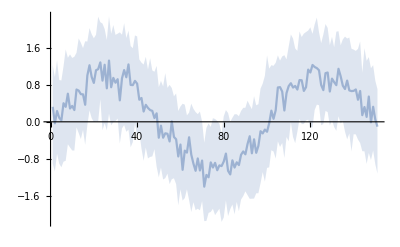

```mathematica
HHListLinePlotMean[ testData, HHMeanPlot-> Median, HHErrorPlot-> Quartiles]
```

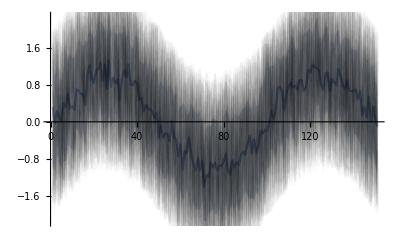

```mathematica
HHListLinePlotMean[ testData, HHMeanPlot-> Median, HHErrorPlot-> Quartiles,
	PlotStyle-> Opacity[0.02,Black]
]
```